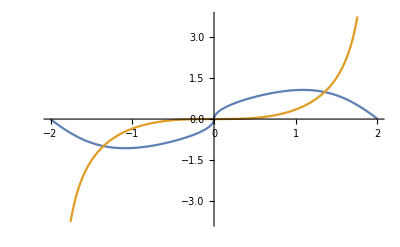

```mathematica
With[{τ=0.001,ζ=0},sol=DSolve[{ϕ'[x]==ϕ[x]^2+x^2,ϕ[τ]==ζ},ϕ,x];d=Denominator[ϕ[x]/.sol[[1]]];e=ϕ[x]/.sol[[1]];Plot[Evaluate[{d,e}],{x,-2,2}]]
```